# Analysis of Packing V3E07L1N01T1_1

Three Vertices, Seven Edges, 1 Loop, Combinatorial Number 01, Face Pattern 1, Type 1

```mathematica
-Graphics-;
```

We use the coordinate method from V3E6L0N2T1_1.  Also, we need α+β = 1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]).  The reasoning for this is as follows.  Suppose α+β = θ.

```mathematica
-Graphics-;
```

The following equation is based on the rhombus in the center of the flat torus.We use the fact that the rhombus breaks into four equal triangles that are all in terms of rb, since we know the relationship between rs and rb.Note that we cannot explicitly solve for rb, rs; trigonometry doesn' t tell us exactly where the sides are broken up between rs and rb, so the triangles could be dilated to any degree while still obeying the same relationships.Thus, solving gives us the angle x, which can be then used to find α.

```mathematica
Solve[{Sin[x]==((-1+√2) (1/2))/((1/2)+(-1+√2) (1/2)),Tan[x]==((-1+√2) (1/2))/(√(((-1+√2) (1/2)+(1/2))^2-((-1+√2) (1/2))^2))},{x}]
```

{{x→ConditionalExpression[ArcTan[(-3+2 √2)/(√(-1+2 √2)-√(2 (-1+2 √2)))]+2 π C[1],C[1]∈ℤ]}}

π = 2 (θ) + 2 (x)

```mathematica
Simplify[(Pi-2(ArcTan[(-3+2 √2)/(√(-1+2 √2)-√(2 (-1+2 √2)))]))/2]
```

1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])

This is θ, or α+β!

```mathematica
Simplify[Solve[α+β == 1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),β]]
```

{{β→1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))}}

Now, we can substitute this into our lattice vectors and circle centers.; the circle centers we are using come from V3E6L0N2T1_1.

## Circle Centers and Radii

```mathematica
centers = Simplify[{{0,0},{(1/Sqrt[2])*Cos[α],(1/Sqrt[2])*Sin[α]},{(1/Sqrt[2])*Cos[-α]+((2/Sqrt[2])(Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))]))*Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))+α],(1/Sqrt[2])*Sin[-α]+((2/Sqrt[2])(Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))]))*Sin[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))+α]}}]
```

{{0,0},{Cos[α]/(√2),Sin[α]/(√2)},{-(-2 Cos[α]+Cos[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]])/(√2),Sin[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]/(√2)}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = 
 Simplify[{{(2/Sqrt[2])*Cos[α],0},
{ ((2 /√2 )*Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))] )*Cos[α+1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))],((2 /√2 )*Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))] )*Sin[α+1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))]}}]
```

{{√2 Cos[α],0},{(-1+√2) Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]],√(-1+2 √2) Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]}}

We need the length of w2 to be greater than 1:

```mathematica
Simplify[Sqrt[(((2 /√2 )*Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))] )*Cos[α+1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))])^2+(((2 /√2 )*Cos[1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))] )*Sin[α+1/2 (π-2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))]))])^2]]
```

√2 √(Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]^2)

When does this equal 1 (so that we will have a lower bound on α)?

```mathematica
Simplify[Solve[√2 √(Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]^2)==1,α]]
```

{{α→ConditionalExpression[-π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[(3 π)/4-ArcTan[(-1+√2)/(√(-1+2 √2))]+2 π C[1],C[1]∈ℤ]},{α→ConditionalExpression[(5 π)/4-ArcTan[(-1+√2)/(√(-1+2 √2))]+2 π C[1],C[1]∈ℤ]}}

```mathematica
N[Simplify[Solve[√2 √(Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]^2)==1,α]]]
```

{{α→ConditionalExpression[-1.08265+6.28319 C[1],C[1]∈ℤ]},{α→ConditionalExpression[0.488147+6.28319 C[1],C[1]∈ℤ]},{α→ConditionalExpression[2.05894+6.28319 C[1],C[1]∈ℤ]},{α→ConditionalExpression[3.62974+6.28319 C[1],C[1]∈ℤ]}}

So α  -> π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{2,3,0,0},{2,1,0,1},{2,1,1,0},{3,1,0,1},{3,1,1,1},{3,1,1,0}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,
P1:= centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]];
P2:= centers[[edges[[i,1]] ]];
Print["Edge ",i,": Length is ",
Sqrt[FullSimplify[(P1[[1]]-P2[[1]])^2+(P1[[2]]-P2[[2]])^2,{0≤α≤ Pi/2}]]];
]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is √(3-2 √2)

Edge 3: Length is 1/(√2)(√(Cos[α]^2+Sin[α]^2+2 ((-2+√2) Cos[α]-√(-2+4 √2) Sin[α]) Sin[α+ArcTan[√(1/7 (-5+4 √2))]]+4 Sin[α+ArcTan[√(1/7 (-5+4 √2))]]^2))

Edge 4: Length is 1/(√2)

$Aborted

```mathematica
Plot[1/(√2)(√(Cos[α]^2+Sin[α]^2+2 ((-2+√2) Cos[α]-√(-2+4 √2) Sin[α]) Sin[α+ArcTan[√(1/7 (-5+4 √2))]]+4 Sin[α+ArcTan[√(1/7 (-5+4 √2))]]^2)),{α,0,2Pi}]
```

-Graphics-

```mathematica
Plot[1/2 √((-2 √2 Cos[α]+√2 Cos[α+2 ArcTan[√(1/7 (-5+4 √2))]]+2 (-1+√2) Sin[α+ArcTan[√(1/7 (-5+4 √2))]])^2+(-2 √(-1+2 √2) Sin[α+ArcTan[√(1/7 (-5+4 √2))]]+√2 Sin[α+2 ArcTan[√(1/7 (-5+4 √2))]])^2),{α,0,2Pi}]
```

-Graphics-

```mathematica
Plot[√(1/2-Cos[2 (α+ArcTan[√(1/7 (-5+4 √2))])]+√(-1/2+√2) Cos[2 α+3 ArcTan[√(1/7 (-5+4 √2))]]+(1-1/(√2)) Sin[2 α+3 ArcTan[√(1/7 (-5+4 √2))]]),{α,0,2Pi}]
```

-Graphics-

Because some of the edge lengths were not cooperating, plotting these edge lengths quickly shows that these lengths are constant and the correct lengths.

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/4,"α"},π/4-ArcTan[(-1+√2)/(√(-1+2 √2))],Pi/4},AnimationRunning -> False
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,Pi/4,"α"},π/4-ArcTan[(-1+√2)/(√(-1+2 √2))],Pi/4},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_1→Csc[2 α] Sin[2 ArcTan[(-1+√2)/(√(-1+2 √2))]] ω_2+1/2 (-2+√(-2+4 √2) Csc[α] Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]-(-2+√2) Sec[α] Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]) ω_3,ω_4→1/2 ((-2+Cos[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]] Sec[α]+Csc[α] Sin[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]) ω_2+(√(-2+4 √2) Csc[α]+(-2+√2) Sec[α]) Sin[α+ArcTan[(-1+√2)/(√(-1+2 √2))]] ω_3),ω_6→(√2 Csc[α+ArcTan[(-1+√2)/(√(-1+2 √2))]] Sin[2 ArcTan[(-1+√2)/(√(-1+2 √2))]] ω_2+2 (-√(-1+2 √2) Cos[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]+(1-√2+√2 Cos[α] Csc[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]) Sin[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]) ω_5)/(2 (√(-1+2 √2) Cos[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]+(-1+√2) Sin[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]])),ω_7→(Csc[α+ArcTan[(-1+√2)/(√(-1+2 √2))]] Csc[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]] ((-2+√2) √(-1+2 √2) Cos[2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))])]+(4-3 √2) Sin[2 (α+ArcTan[(-1+√2)/(√(-1+2 √2))])]) ω_2-2 Cos[α] (√2 Csc[α+ArcTan[(-1+√2)/(√(-1+2 √2))]]-2 √(-1+2 √2) Csc[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]) ω_5)/(2 (-1+√2+√(-1+2 √2) Cot[α+2 ArcTan[(-1+√2)/(√(-1+2 √2))]]))}

Notice that stress ω_2, ω_3, ω_5 is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{Subscript[ω, 2]-> 1,Subscript[ω, 5]-> 1,Subscript[ω, 3]-> 1, α->Pi/4}]]
```

{{0.,0.},{0.,0.},{0.,0.}}

For every α and β in the feasible region (for all Pi/2+ArcCos[2 (-1+√2)]/2< α <  Pi and  Pi/2+ArcCos[2 (-1+√2)]/2<  β < Pi and α >β)  we need to make sure that all ω_i are positive for some choice of ω_1. Try ω_1=1

```mathematica
N[Simplify[stresses/.{Subscript[ω, 6]-> 1,Subscript[ω, 4]-> 1,Subscript[ω, 3]-> 1}]]
```

{ω_1→0.5 (-2.+1.91229 Csc[α] Sin[0.297251+α]+0.585786 Sec[α] Sin[0.297251+α])+0.560097 Csc[2. α] ω_2,1.→0.5 ((1.91229 Csc[α]-0.585786 Sec[α]) Sin[0.297251+α]+(-2.+Cos[0.594503+α] Sec[α]+Csc[α] Sin[0.594503+α]) ω_2),1.→(0.5 (0.792097 Csc[0.297251+α] ω_2+2. (-1.35219 Cos[0.594503+α]+(-0.414214+1.41421 Cos[α] Csc[0.297251+α]) Sin[0.594503+α]) ω_5))/(1.35219 Cos[0.594503+α]+0.414214 Sin[0.594503+α]),ω_7→(0.5 (Csc[0.297251+α] Csc[0.594503+α] (-0.792097 Cos[2. (0.297251+α)]-0.242641 Sin[2. (0.297251+α)]) ω_2-2. Cos[α] (1.41421 Csc[0.297251+α]-2.70439 Csc[0.594503+α]) ω_5))/(0.414214+1.35219 Cot[0.594503+α])}

```mathematica
guts := Simplify[Union[{0},Table[Subscript[ω, i]/.stresses,(*first list all of the right hand sides of all the stresses*)
{i,Length[edges]}]/.{Subscript[ω, 2]-> .1,Subscript[ω, 5]-> .1,Subscript[ω, 3]-> .1}]]
```

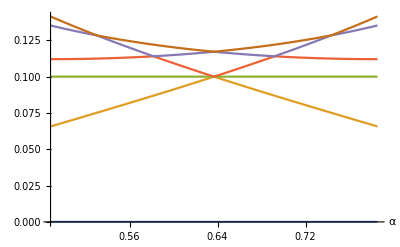

```mathematica
Plot[guts,{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))],Pi/4},RegionFunction->Function[{α,β},α>β],AxesLabel->Automatic]
```

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{α,β},Reals],π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]<α<Pi/4}]
```

ArcCos[1-1/(√2)]

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{α,β},Reals],π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]<α<Pi/4}]
```

Sec[α] Sin[α+ArcTan[√(1/7 (-5+4 √2))]]

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

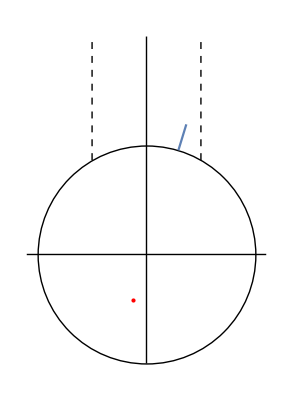

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2,Pi/4}],
(*bounds come from only taking half of the region to aviod duplication*)
]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{α},Reals],π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]<α<Pi/4}]
```

((7-4 √2) π Csc[α+ArcTan[√(1/7 (-5+4 √2))]] Sec[α])/(4 √(-2+4 √2))

Plot the density over the parameter space

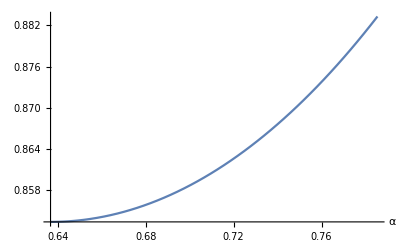

```mathematica
Plot[torusDensity,{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2,Pi/4},AxesLabel->Automatic]
```

Color the moduli space region with color depending on the density. Red shade is close to 1 and Blue shade is close to .5

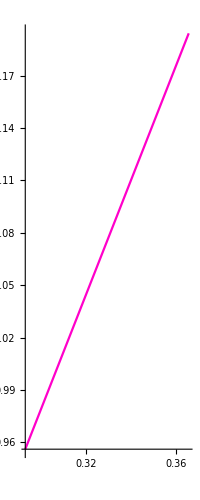

```mathematica
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2,Pi/4},ColorFunction->(Hue[torusDensity]/.{α ->#3,β->#4} &),ColorFunctionScaling->False,BoundaryStyle->Directive[Black,Thick,Dashed],Mesh->None]
```

Now find the minimum density with in the region.

```mathematica
NMinimize[{torusDensity,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2< α && α < Pi/4 },{{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2,Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.8533487099264552297358746539113749001429,{α→0.6367724827368449066392493242557044333781}}

```mathematica
NMaximize[{torusDensity,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2< α && α < Pi/4 },{{α,π/4-ArcTan[(-1+√2)/(√(-1+2 √2))]1/2,Pi/4}},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

{0.88331053808648840173050934060636024001,{α→0.7853981633974483096156608458198757210493}}